```mathematica
net = NetGraph[{ElementwiseLayer[Ramp]}, {}]
```

NetGraph[]

```mathematica
net[{-1, 0, 1}]
```

{0.,0.,1.}

```mathematica
net = NetGraph[{LinearLayer[3], LinearLayer[5]}, {1-> 2}, "Input"-> 2]
```

NetGraph[]

```mathematica
net = NetInitialize[net];
```

```mathematica
net[{1.0, 2.0}]
```

{0.578659,1.74188,-1.98467,0.111787,1.36843}

```mathematica
net = NetGraph[<|"linear1"->LinearLayer[3], "linear2"-> LinearLayer[4]|>, {"linear1"-> "linear2"}]
```

NetGraph[]

```mathematica
NetExtract[net, "linear2"]
```

LinearLayer[<>]

```mathematica
Part[net, "linear1"]
```

LinearLayer[<>]

```mathematica
net = NetGraph[{Ramp, Tanh, Times,Plus}, {1 -> 2 -> 3, 1 ->3 -> 4, 2 -> 4}]
```

NetGraph[]

```mathematica
net[{-2, -1, 0, 1, 2}]
```

{0.,0.,0.,1.52319,2.89208}

```mathematica
net = NetGraph[{2, Ramp, 4, Ramp, 8}, {1 -> 2 -> 3 -> 4 -> 5}]
```

NetGraph[]

```mathematica
NetChain[{2, Ramp, 4, Ramp, 8}]
```

NetChain[]

```mathematica
net = NetGraph[{Ramp, LogisticSigmoid}, {1->2, 1->NetPort["Output1"], 2-> NetPort["Output2"]}]
```

NetGraph[]

```mathematica
net[{-1, 0, 1}]
```

<|Output1→{0.,0.,1.},Output2→{0.5,0.5,0.731059}|>

```mathematica
net[{-1, 0, 1}, "Output1"]
```

{0.,0.,1.}

```mathematica
subnet = Take[net, {NetPort["Input"], NetPort["Output2"]}]
```

NetGraph[]

```mathematica
subnet[{-1, 0, 1}]
```

```mathematica
net = NetGraph[{Ramp, LogisticSigmoid, CatenateLayer[]}, {1->2, {1, 2} -> 3}]
```

NetGraph[]

```mathematica
net = NetGraph[{Ramp, LogisticSigmoid, TotalLayer[]}, {NetPort["Input1"]->1, NetPort["Input2"]->2, {1, 2} -> 3}]
```

NetGraph[]

```mathematica
net[<|"Input1"-> {-1, 0, 1}, "Input2"->{1, 2, 3}|>]
```

{0.731059,0.880797,1.95257}

```mathematica
net = NetGraph[{LinearLayer[2], SoftmaxLayer[], MeanSquaredLossLayer[]},
{1->2->3}, "Input"->"Scalar"]
```

NetGraph[]

```mathematica
net = NetInitialize[net];
```

```mathematica
net[<|"Input"->1, "Target"-> {2, 3}|>]
```

4.3113

```mathematica
net = NetGraph[{Ramp, SoftmaxLayer[]}, {1->2}, "Output"->NetDecoder[{"Class", {"a", "b"}}]]
```

NetGraph[]

```mathematica
net[{0.2, 0.8}]
```

b

```mathematica
net[{0.5, 0.4}]
```

a

```mathematica
net[{0.8, 0.2}, "Probabilities"]
```

<|a→0.645656,b→0.354344|>

```mathematica
net[{0.5, 0.4}, {"Probability", "a"}]
```

0.524979

```mathematica
net[{0.8, 0.2}, "Entropy"]
```

0.650094

```mathematica
net = NetGraph[{2, 4, 8, Tanh}, {1->2-> 3->4}]
```

NetGraph[]

```mathematica
Take[net, {3,4}]
```

NetGraph[]

```mathematica
obj = ResourceObject["CIFAR-100"]
```

ResourceObject[…]

```mathematica
trainingData = ResourceData[obj, "TrainingDataset"];
RandomSample[trainingData, 5]
```

Dataset[<>]

```mathematica
labels = Union @ Normal @trainingData[All, "Label"]
```

{aquatic mammals,fish,flowers,food containers,fruit and vegetables,household electrical devices,household furniture,insects,large carnivores,large man-made outdoor things,large natural outdoor scenes,large omnivores and herbivores,medium-sized mammals,non-insect invertebrates,people,reptiles,small mammals,trees,vehicles 1,vehicles 2}

```mathematica
sublabels = Union @ Normal @trainingData[All, "SubLabel"]
```

{apple,aquarium fish,baby,bear,beaver,bed,bee,beetle,bicycle,bottle,bowl,boy,bridge,bus,butterfly,camel,can,castle,caterpillar,cattle,chair,chimpanzee,clock,cloud,cockroach,computer keyboard,couch,crab,crocodile,cup,dinosaur,dolphin,elephant,flatfish,forest,fox,girl,hamster,house,kangaroo,lamp,lawn-mower,leopard,lion,lizard,lobster,man,maple tree,motorcycle,mountain,mouse,mushroom,oak tree,orange,orchid,otter,palm tree,pear,pickup truck,pine tree,plain,plate,poppy,porcupine,possum,rabbit,raccoon,ray,road,rocket,rose,sea,seal,shark,shrew,skunk,skyscraper,snail,snake,spider,squirrel,streetcar,sunflower,sweet pepper,table,tank,telephone,television,tiger,tractor,train,trout,tulip,turtle,wardrobe,whale,willow tree,wolf,woman,worm}

```mathematica
convnet = NetChain[{
ConvolutionLayer[20, 5], Ramp, PoolingLayer[2, 2],
ConvolutionLayer[50, 5], Ramp, PoolingLayer[2, 2],
500, Ramp
},
"Input"->NetEncoder[{"Image", {32, 32}}]]
```

NetChain[]

```mathematica
net=NetGraph[{convnet,100,SoftmaxLayer[],20,SoftmaxLayer[]},{NetPort["Image"]->1->2->3->NetPort["SubLabel"],2->4->5->NetPort["Label"]},"Label"->NetDecoder[{"Class",labels}],"SubLabel"->NetDecoder[{"Class",sublabels}]]
```

NetGraph[]

```mathematica
trained = NetTrain[net, trainingData];
```

```mathematica
chain = NetChain[{Ramp, LogisticSigmoid}];
NetGraph[{chain, LinearLayer[3]}, {1->2}]
```

NetGraph[]

```mathematica
net = NetGraph[{Ramp, LogisticSigmoid, CatenateLayer[]}, {1->2, {1, 2}->3}];
NetChain[{ElementwiseLayer[Ramp], net}]
```

NetChain[]

```mathematica
net = NetGraph[{1, Ramp, 2, Tanh}, {1->2-> 3-> 4}]
```

NetGraph[]

```mathematica
Normal[net]
```

{LinearLayer[<>],ElementwiseLayer[<>],LinearLayer[<>],ElementwiseLayer[<>]}

```mathematica
net = NetGraph[{LinearLayer[2], Ramp, LinearLayer[3],SoftmaxLayer[], MeanSquaredLossLayer[]}, {1->2->3->4->5}, "Input"->"Scalar"]
```

NetGraph[]

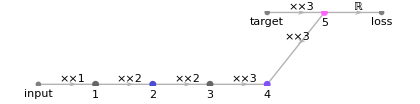

```mathematica
TraditionalForm[net]
```

```mathematica
edges = {NetPort["matrix"]->1, NetPort["vector"]->1}
```

{NetPort[matrix]→1,NetPort[vector]→1}

```mathematica
NetGraph[{DotLayer[]}, edges, "vector"->{2}, "matrix"->{3,2}]
```

NetGraph[]

```mathematica
NetGraph[{DotLayer[]},Reverse[edges],"vector"->{2},"matrix"->{3,2}]
```

NetGraph::valfail: Validation failed for DotLayer: invalid dimensions for input tensors: {2} and {3, 2}.

$Failed